FittedModel[Piecewise[{{0.676408, x<103.}, {2.00131, x≥103.}, {0, True}}]]

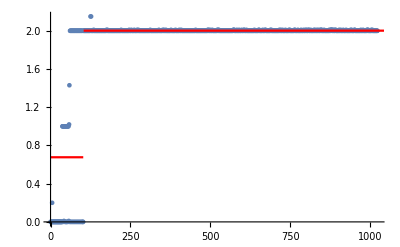

0.979792

{6.34389×10^-108,0.,1.33743737054×10^-864}

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "regexMult-nq"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, Piecewise[{{a,x<b},{c,x≥b}}],{a,{b,103},c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
nlm["ParameterPValues"]
```